C:\Users\mouze\Desktop\rpk2\lab1\lab1

StringContainsQ::strse: A string or list of strings is expected at position 1 in StringContainsQ[List,x].

StringContainsQ::strse: A string or list of strings is expected at position 1 in StringContainsQ[List,y].

StringContainsQ::strse: A string or list of strings is expected at position 1 in StringContainsQ[List,u].

General::stop: Further output of StringContainsQ::strse will be suppressed during this calculation.

-Graphics3D-

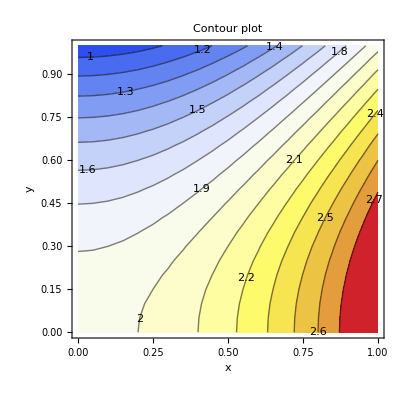

-Graphics3D--Graphics-

```mathematica
(* Чтение результатов МКЭ из lab1_result.txt и построение 3D графика *)
SetDirectory[NotebookDirectory[]]
(* --- читаем файл --- *)
file = "lab1_result.txt";
lines = Import[file, "Lines"];

(* находим строку после заголовка таблицы "Узел  x  y  u" *)
startLine = First @ Flatten @ Position[lines, s_ /; StringContainsQ[s, "x"] && StringContainsQ[s, "y"] && StringContainsQ[s, "u"]];

(* берём только строки с данными — цифры после разделителя "---" *)
dataLines = Select[
    Drop[lines, startLine],
    StringMatchQ[#, RegularExpression["\\s*\\d+.*"]] &
];

(* парсим: узел, x, y, u *)
data = ToExpression @ StringSplit[#] & /@ dataLines;
pts  = {#[[2]], #[[3]], #[[4]]} & /@ data;

(* --- 3D график --- *)
fig = ListPlot3D[
    pts,
    PlotRange   -> All,
    ColorFunction -> "TemperatureMap",
    ColorFunctionScaling -> True,
    Mesh        -> {20, 20},
    MeshStyle   -> Directive[GrayLevel[0.6], Opacity[0.3]],
    AxesLabel   -> {"x", "y", "u"},
    PlotLabel   -> Style["FEM solution:  ∇(λ∇u) + q = 0", 14, Bold],
    BoxRatios   -> {1, 1, 0.6},
    ImageSize   -> 600
]

(* --- контурный график сверху --- *)
fig2 = ListContourPlot[
    {#[[1]], #[[2]], #[[3]]} & /@ pts,
    ColorFunction  -> "TemperatureMap",
    Contours       -> 15,
    ContourLabels  -> True,
    FrameLabel     -> {{"y", None}, {"x", None}},
    PlotLabel      -> Style["Contour plot", 13, Bold],
    ImageSize      -> 400
]

(* --- вывод рядом --- *)
Row[{fig, fig2}, Spacer[20]]
```